```mathematica
{x,Sin[x]}.RotationMatrix[2π-π/4]
```

{x/(√2)-Sin[x]/(√2),x/(√2)+Sin[x]/(√2)}

```mathematica
√(1+f'[x]^2)(f[x]±Sin[f[x]])
```

(f[x]±Sin[f[x]]) √(1+f'[x]^2)

```mathematica
With[{f=Function[x,x x]},
√(1+f'[x]^2)(f[x]±Sin[f[x]])
]
```

√(1+4 x^2) (x^2±Sin[x^2])

```mathematica
ExpandAll[√(1+4 x^2) (x^2±Sin[x^2])]
```

√(1+4 x^2) (x^2±Sin[x^2])

```mathematica
(f[x]±Sin[f[x]])/(√(1+f'[x]^2))
```

(f[x]±Sin[f[x]])/(√(1+f'[x]^2))

```mathematica
(f[x]±Sin[f[x]])/(∫_0^1 √(1+f'[x]^2)ⅆx)
```

(f[x]±Sin[f[x]])/(∫_0^1 √(1+f'[x]^2)ⅆx)

```mathematica
(f[x]±Sin[l[f[x]]])/(∫_0^1 √(1+f'[x]^2)ⅆx)
```

(f[x]±Sin[l[f[x]]])/(∫_0^1 √(1+f'[x]^2)ⅆx)

```mathematica
With[{f=0},
(f[x]±Sin[l[f[x]]])/(∫_0^1 √(1+f'[x]^2)ⅆx)
]
```

0[x]±Sin[l[0[x]]]

```mathematica
With[{f=Function[x,0]},
(f[x]±Sin[l[f[x]]])/(∫_0^1 √(1+f'[x]^2)ⅆx)
]
```

0±Sin[l[0]]

```mathematica
With[{f=Function[x,x]},
(f[x]±Sin[l[f[x]]])/(∫_0^1 √(1+f'[x]^2)ⅆx)
]
```

(x±Sin[l[x]])/(√2)

```mathematica
With[{f=Function[x,x]},
(f[x]±Sin[f[x]])/(∫_0^1 √(1+f'[x]^2)ⅆx)
]
```

(x±Sin[x])/(√2)

```mathematica
With[{f=Function[x,0]},
(f[x]±Sin[f[x]])/(∫_0^1 √(1+f'[x]^2)ⅆx)
]
```

0±0

```mathematica
With[{f=Function[x,0]},
(f[x]±Sin[x])/(∫_0^1 √(1+f'[x]^2)ⅆx)
]
```

0±Sin[x]

```mathematica
With[{f=Function[x,x]},
(f[x]±Sin[x])/(∫_0^1 √(1+f'[x]^2)ⅆx)
]
```

(x±Sin[x])/(√2)

```mathematica
With[{f=Function[x,2x]},
(f[x]±Sin[x])/(∫_0^1 √(1+f'[x]^2)ⅆx)
]
```

(2 x±Sin[x])/(√5)

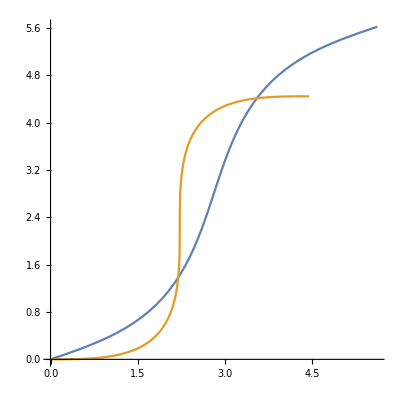

```mathematica
ParametricPlot[{
{(2x+Sin[x])/(√5),(2x-Sin[x])/(√5)},
{(x+Sin[x])/(√2),(x-Sin[x])/(√2)}
},{x,0,2π}]
```

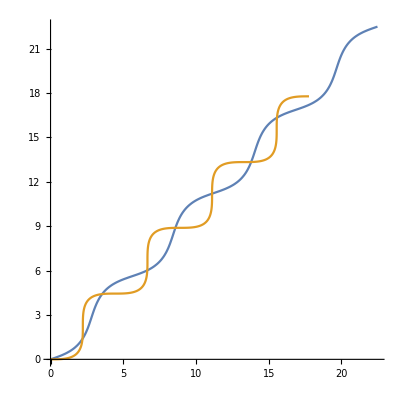

```mathematica
ParametricPlot[{
{(2x+Sin[x])/(√5),(2x-Sin[x])/(√5)},
{(x+Sin[x])/(√2),(x-Sin[x])/(√2)}
},{x,0,8π}]
```

```mathematica
With[{f=Function[x,2x]},
(f[x]±Sin[∫_0^1 √(1+f'[x]^2)ⅆx x])/(∫_0^1 √(1+f'[x]^2)ⅆx)
]
```

Integrate::diffend: ∫_0^1 √(1+f'[x]^2)ⅆxx cannot be interpreted since ⅆx is followed by x. It may be necessary to use parentheses to ensure that ⅆx appears at the end of the integral.

```mathematica
With[{f=Function[x,2x]},
(f[x]±Sin[x∫_0^1 √(1+f'[x]^2)ⅆx ])/(∫_0^1 √(1+f'[x]^2)ⅆx)
]
```

(2 x±Sin[√5 x])/(√5)

```mathematica
With[{f=Function[x,x]},
(f[x]±Sin[x∫_0^1 √(1+f'[x]^2)ⅆx ])/(∫_0^1 √(1+f'[x]^2)ⅆx)
]
```

(x±Sin[√2 x])/(√2)

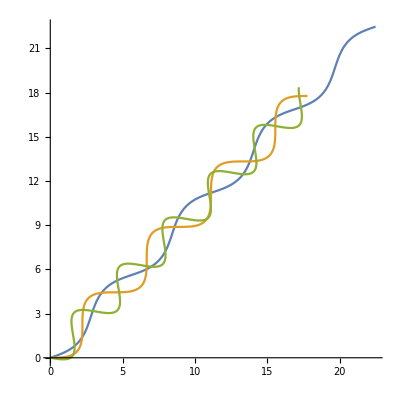

```mathematica
ParametricPlot[{
{(2x+Sin[x])/(√5),(2x-Sin[x])/(√5)},
{(x+Sin[x])/(√2),(x-Sin[x])/(√2)},
{(x+Sin[√2 x])/(√2),(x-Sin[√2 x])/(√2)}
},{x,0,8π}]
```

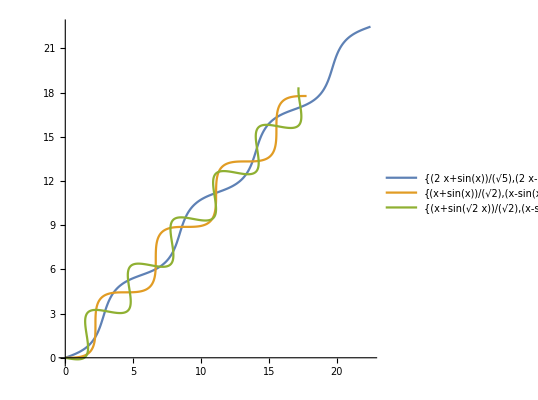

```mathematica
ParametricPlot[{
{(2x+Sin[x])/(√5),(2x-Sin[x])/(√5)},
{(x+Sin[x])/(√2),(x-Sin[x])/(√2)},
{(x+Sin[√2 x])/(√2),(x-Sin[√2 x])/(√2)}
},{x,0,8π},PlotLegends->"Expressions"]
```

```mathematica
Manipulate[
ParametricPlot[{
{(2x+Sin[x])/(√5),(2x-Sin[x])/(√5)},
{(x+Sin[x])/(√2),(x-Sin[x])/(√2)},
{(x+Sin[√2 x])/(√2),(x-Sin[√2 x])/(√2)},
{x,Sin[x]},
{x,-x+a}
},{x,0,8π},PlotLegends->"Expressions"]
,{a,0,10}]
```

```mathematica
With[{f=Function[x,x^2]},
(f[x]±Sin[x∫_0^1 √(1+f'[x]^2)ⅆx ])/(∫_0^1 √(1+f'[x]^2)ⅆx)
]
```

(4 (x^2±Sin[1/4 x (2 √5+ArcSinh[2])]))/(2 √5+ArcSinh[2])

```mathematica
With[{f=Function[x,x^2]},
{(f[x]+Sin[x∫_0^1 √(1+f'[x]^2)ⅆx ])/(∫_0^1 √(1+f'[x]^2)ⅆx),(f[x]-Sin[x∫_0^1 √(1+f'[x]^2)ⅆx ])/(∫_0^1 √(1+f'[x]^2)ⅆx)}
]
```

{(4 (x^2+Sin[1/4 x (2 √5+ArcSinh[2])]))/(2 √5+ArcSinh[2]),(4 (x^2-Sin[1/4 x (2 √5+ArcSinh[2])]))/(2 √5+ArcSinh[2])}

```mathematica
Manipulate[
ParametricPlot[{
{(2x+Sin[x])/(√5),(2x-Sin[x])/(√5)},
{(x+Sin[x])/(√2),(x-Sin[x])/(√2)},
{(x+Sin[√2 x])/(√2),(x-Sin[√2 x])/(√2)},
{x,Sin[x]},
{x,-x+a},
{(4 (x^2+Sin[1/4 x (2 √5+ArcSinh[2])]))/(2 √5+ArcSinh[2]),(4 (x^2-Sin[1/4 x (2 √5+ArcSinh[2])]))/(2 √5+ArcSinh[2])}
},{x,-8π,8π},PlotLegends->"Expressions"]
,{a,0,10}]
```

```mathematica
With[{f=Function[x,x^2]},
{(f[x]+Sin[x∫_0^x √(1+f'[t]^2)ⅆt ])/(∫_0^x √(1+f'[t]^2)ⅆt),(f[x]-Sin[x∫_0^x √(1+f'[t]^2)ⅆt ])/(∫_0^x √(1+f'[t]^2)ⅆt)}
]
```

{ConditionalExpression[(4 (x^2+Sin[1/4 x (2 x √(1+4 x^2)+ArcSinh[2 x])]))/(2 x √(1+4 x^2)+ArcSinh[2 x]),Re[x]≠0||-1/2<Im[x]<0||0<Im[x]<1/2],ConditionalExpression[(4 (x^2-Sin[1/4 x (2 x √(1+4 x^2)+ArcSinh[2 x])]))/(2 x √(1+4 x^2)+ArcSinh[2 x]),Re[x]≠0||-1/2<Im[x]<0||0<Im[x]<1/2]}

```mathematica
With[{f=Function[x,x^2]},
FullSimplify[{(f[x]+Sin[x∫_0^x √(1+f'[t]^2)ⅆt ])/(∫_0^x √(1+f'[t]^2)ⅆt),(f[x]-Sin[x∫_0^x √(1+f'[t]^2)ⅆt ])/(∫_0^x √(1+f'[t]^2)ⅆt)},Element[x,Reals]]
]
```

{ConditionalExpression[(4 (x^2+Sin[1/4 x (2 x √(1+4 x^2)+ArcSinh[2 x])]))/(2 x √(1+4 x^2)+ArcSinh[2 x]),x≠0],ConditionalExpression[(4 (x^2-Sin[1/4 x (2 x √(1+4 x^2)+ArcSinh[2 x])]))/(2 x √(1+4 x^2)+ArcSinh[2 x]),x≠0]}

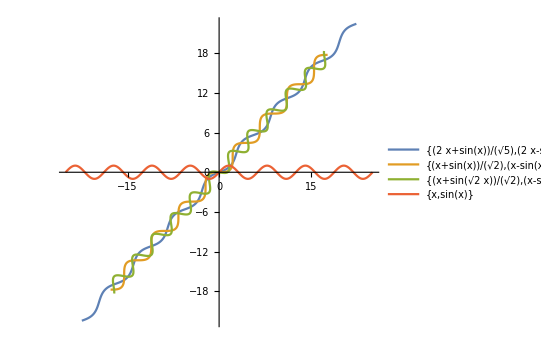

```mathematica
ParametricPlot[{
{(2x+Sin[x])/(√5),(2x-Sin[x])/(√5)},
{(x+Sin[x])/(√2),(x-Sin[x])/(√2)},
{(x+Sin[√2 x])/(√2),(x-Sin[√2 x])/(√2)},
{x,Sin[x]}
},{x,-8π,8π},PlotLegends->"Expressions"]
```

```mathematica
ParametricPlot[{
{(2x+Sin[x])/(√5),(2x-Sin[x])/(√5)},
{(x+Sin[x])/(√2),(x-Sin[x])/(√2)},
(4 (x^2+Sin[1/4 x (2 x √(1+4 x^2)+ArcSinh[2 x])]))/(2 x √(1+4 x^2)+ArcSinh[2 x]),
{x,Sin[x]}
},{x,-8π,8π},PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
{(4 (x^2+Sin[1/4 x (2 x √(1+4 x^2)+ArcSinh[2 x])]))/(2 x √(1+4 x^2)+ArcSinh[2 x]),(4 (x^2-Sin[1/4 x (2 x √(1+4 x^2)+ArcSinh[2 x])]))/(2 x √(1+4 x^2)+ArcSinh[2 x])}
```

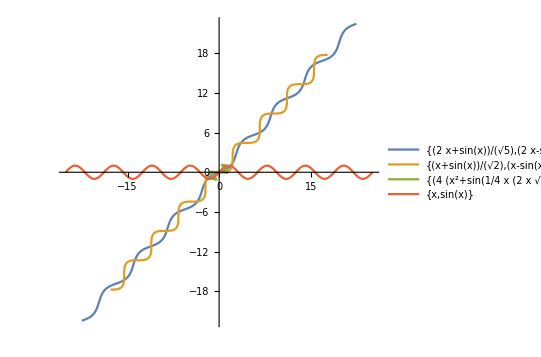

```mathematica
ParametricPlot[{
{(2x+Sin[x])/(√5),(2x-Sin[x])/(√5)},
{(x+Sin[x])/(√2),(x-Sin[x])/(√2)},
{(4 (x^2+Sin[1/4 x (2 x √(1+4 x^2)+ArcSinh[2 x])]))/(2 x √(1+4 x^2)+ArcSinh[2 x]),(4 (x^2-Sin[1/4 x (2 x √(1+4 x^2)+ArcSinh[2 x])]))/(2 x √(1+4 x^2)+ArcSinh[2 x])},
{x,Sin[x]}
},{x,-8π,8π},PlotLegends->"Expressions"]
```